# Initialization

```mathematica
HaToeV=27.21138602;
```

```mathematica
SizeLegend=1.5;
```

```mathematica
SetDirectory["~/Dropbox/Manuscripts/CC4/Data"];
```

```mathematica
Needs["MaTeX`"]
SetOptions[MaTeX,"Preamble"->{"\\usepackage{amssymb,amsmath,latexsym,amsfonts,amsthm,mathpazo,xcolor,bm,mhchem}"}];
```

# XLS

### Methods

```mathematica
Met={"CCSD","CCSDT-3","CC3","CCSDT","CC4","CCSDTQ","CCSDTQP"};
```

### MSE/AVDZ

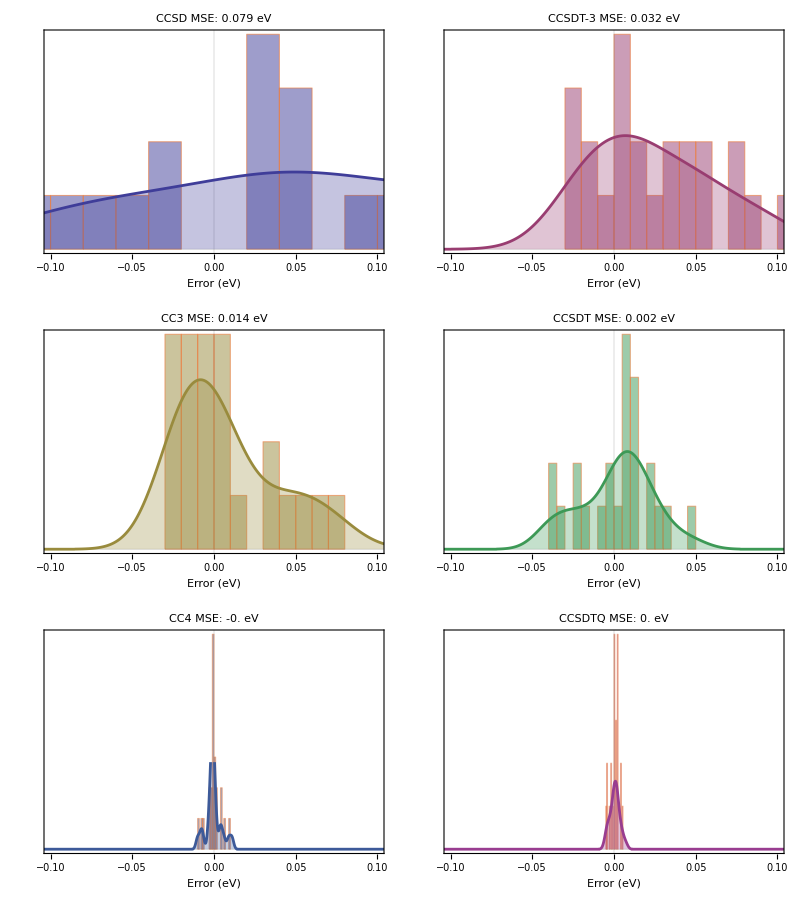

```mathematica
MSEDZ=Import["CC4-Bench.xlsx"]⟦1,4;;28,3;;9⟧;
MSEDZ=Table[MSEDZ⟦a,b⟧-MSEDZ⟦a,Length[Met]⟧,{a,Length[MSEDZ]},{b,Length[Met]-1}];
graph=Table[
Show[{
Histogram[MSEDZ⟦2;;,m⟧,20,"PDF",PlotTheme->"Scientific",BaseStyle->14,PlotRange->{{-0.1,0.1},Automatic},FrameLabel->{"Error (eV)",None},ChartStyle->{Directive[Opacity[0.5],ColorData[1,"ColorList"]⟦m⟧]},FrameTicks->{Automatic,None},PlotLabel->Style[Met⟦m⟧<>" MSE: "<>ToString[SetAccuracy[Mean[MSEDZ⟦2;;,m⟧],4]]<>" eV",12]]
,
SmoothHistogram[DeleteCases[MSEDZ⟦2;;,m⟧,""],Automatic,"PDF",PlotRange->{{-1,1},Automatic},PlotStyle->Directive[ColorData[1,"ColorList"]⟦m⟧,Thickness[0.01]],Filling->Bottom,PlotTheme->"Web"]
},ImageSize->200]
,{m,Length[Met]-1}];
Grid[{graph⟦1;;2⟧,graph⟦3;;4⟧,graph⟦5;;6⟧}]
Export["histograms_MSE_AVDZ.pdf",%];
```

### MAE/AVDZ

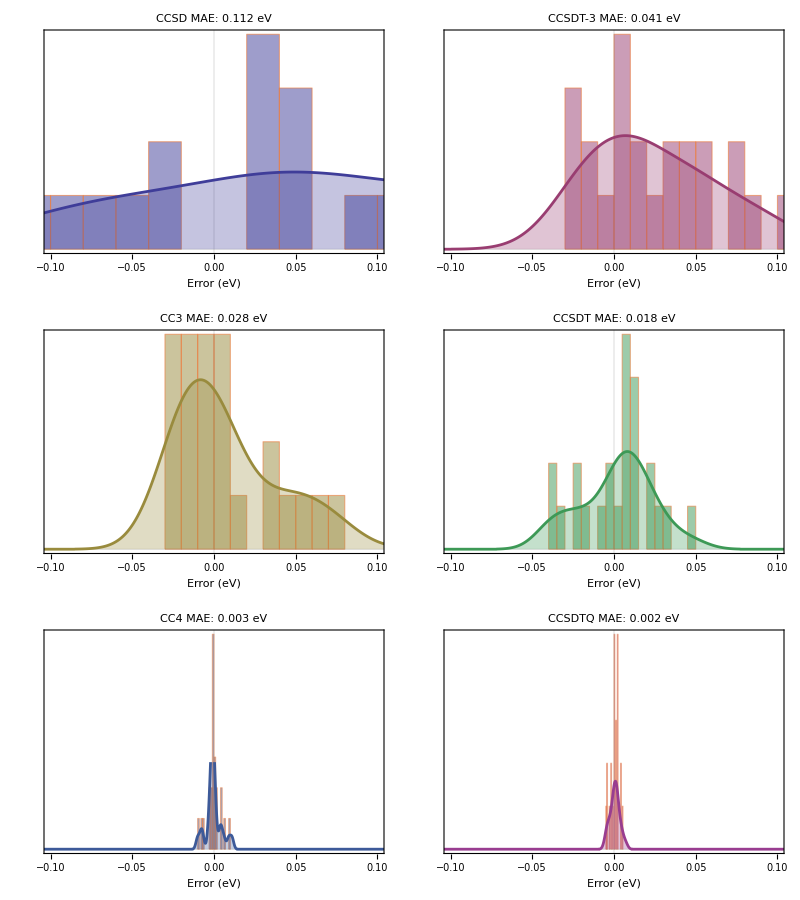

```mathematica
MAEDZ=Import["CC4-Bench.xlsx"]⟦1,4;;28,3;;9⟧;
MAEDZ=Table[MAEDZ⟦a,b⟧-MAEDZ⟦a,Length[Met]⟧,{a,Length[MAEDZ]},{b,Length[Met]-1}];
graph=Table[
Show[{
Histogram[MAEDZ⟦2;;,m⟧,20,"PDF",PlotTheme->"Scientific",BaseStyle->14,PlotRange->{{-0.1,0.1},Automatic},FrameLabel->{"Error (eV)",None},ChartStyle->{Directive[Opacity[0.5],ColorData[1,"ColorList"]⟦m⟧]},FrameTicks->{Automatic,None},PlotLabel->Style[Met⟦m⟧<>" MAE: "<>ToString[SetAccuracy[Mean[Abs[MAEDZ⟦2;;,m⟧]],4]]<>" eV",12]]
,
SmoothHistogram[DeleteCases[MAEDZ⟦2;;,m⟧,""],Automatic,"PDF",PlotRange->{{-1,1},Automatic},PlotStyle->Directive[ColorData[1,"ColorList"]⟦m⟧,Thickness[0.01]],Filling->Bottom,PlotTheme->"Web"]
},ImageSize->200]
,{m,Length[Met]-1}];
Grid[{graph⟦1;;2⟧,graph⟦3;;4⟧,graph⟦5;;6⟧}]
Export["histograms_MAE_AVDZ.pdf",%];
```